```mathematica
fc = 1300;
fd = 39200;
```

```mathematica
fc = 1700;
fd = 9600;
```

```mathematica
w = N[2*Pi*fc/fd]
Dd = N[fd/fc/4]-7
```

0.208371

0.538462

```mathematica
0.96886 /(4*Dd)
1-Dd
```

0.449828

0.461538

```mathematica
b1 = (-(1-2*Dd)*Cos[w]+√((1-2*Dd)^2*(Cos[w])^2+4*Dd*(1-Dd)))/(2*(1-Dd));
b2 = (-(1-2*Dd)*Cos[w]-√((1-2*Dd)^2*(Cos[w])^2+4*Dd*(1-Dd)))/(2*(1-Dd));
N[b1]
N[b2]
```

1.16473

-1.00167

```mathematica
b/2^m<1
```

```mathematica
b1/2^2
```

0.291182

```mathematica
data = Transpose[Import["C:/Users/user/PycharmProjects/pythonProject1/out.csv"]][[1]];
```

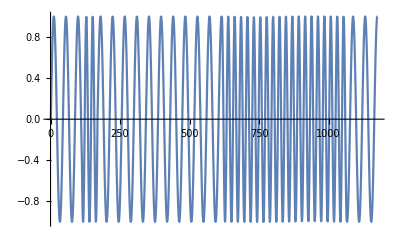

```mathematica
ListLinePlot[data]
```

```mathematica
dataoff7 = data[[7;;]];
dataoff8 = data[[8;;]];
b = 1.1647269329098717;
```

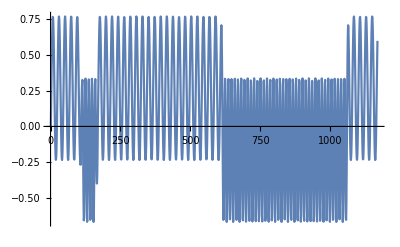

```mathematica
(*y[n_]:=data⟦n⟧*(data⟦n⟧+b*data⟦n-8⟧)/2;*)
y[n_]:=data⟦n⟧*data⟦n-7⟧;
res = Table[y[n], {n, 8, Length[data]}];
ListLinePlot[res]
```

ω=2π F_c/F_d=0.208371
D=F_d/F_c/4=7.538462
β=(-(1-2D)cos(ω)±√((1-2D)^2(cos(ω))^2+4D(1-D)))/(2(1-D))=1.16473; -1.00167